```mathematica
β[x_,y_]:=Piecewise[{{x^2+y^2+1,x^2+y^2≤1/4},{b,x^2+y^2>1/4}}]//PiecewiseExpand
u[x_,y_]:=Piecewise[{{x^2+y^2,x^2+y^2≤1/4},{1/4(1-1/(8b)-1/b)+1/b(((√(x^2+y^2))^4)/2+(√(x^2+y^2))^2)+C Log[2 √(x^2+y^2)],x^2+y^2>1/4}}]//PiecewiseExpand
```

```mathematica
β[r_]:=Piecewise[{{r^2+1,r≤1/2},{b,r>1/2}}]//PiecewiseExpand
u[r_]:=Piecewise[{{r^2,r≤1/2},{1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],r>1/2}}]//PiecewiseExpand
```

```mathematica
FL=D[β[r]u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
2 (r+2 r^3)/.r->1/2
(b C+2 r^2+2 r^4)/r/.r->1/2/.b->10^-3/.C->1/10
```

Piecewise[{{Indeterminate, r==1/2}, {2 (r+2 r^3), r<1/2}, {(b C+2 r^2+2 r^4)/r, True}}]

6251/5000

805/4

3/2

6251/5000

```mathematica
FL=D[u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
```

Piecewise[{{Indeterminate, r==1/2}, {2 r, r<1/2}, {(b C+2 r^2+2 r^4)/(b r), True}}]

6251/5

161/800

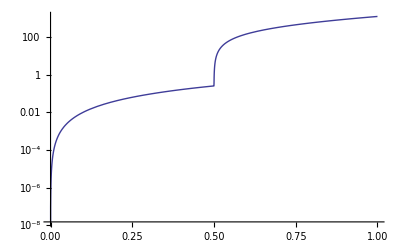

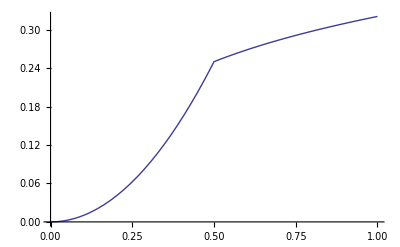

```mathematica
LogPlot[u[r]/.b->10^-3/.C->0.1,{r,0,1}]
Plot[u[r]/.b->10^3/.C->0.1,{r,0,1}]
```

```mathematica
D[β[x,y]D[u[x,y],x],x]+D[β[x,y]D[u[x,y],y],y]//PiecewiseExpand
```

4 (1+2 x^2+2 y^2)

```mathematica
u[1,0]
```

1/4 (1-9/(8 b))+3/(2 b)+C Log[2]

```mathematica
Luxy=Div[{{a[x,y] ,0},{0,b[x,y]}}.Grad[u[x,y],{x,y}, "Cartesian"],{x,y}, "Cartesian"]
Lurt=Div[{{a[r,θ] ,0},{0,b[r,θ]}}.Grad[u[r,θ],{r,θ}, "Polar"],{r,θ}, "Polar"]
```

b^(0,1)[x,y] u^(0,1)[x,y]+b[x,y] u^(0,2)[x,y]+a^(1,0)[x,y] u^(1,0)[x,y]+a[x,y] u^(2,0)[x,y]

a^(1,0)[r,θ] u^(1,0)[r,θ]+((b^(0,1)[r,θ] u^(0,1)[r,θ])/r+(b[r,θ] u^(0,2)[r,θ])/r+a[r,θ] u^(1,0)[r,θ])/r+a[r,θ] u^(2,0)[r,θ]

```mathematica
Div[{{r^2+1 ,0},{0,r^2+1}}.Grad[r^2,{r,θ}, "Polar"],{r,θ}, "Polar"]//Simplify
Div[{{x^2+y^2+1 ,0},{0,x^2+y^2+1}}.Grad[x^2+y^2,{x,y}, "Cartesian"],{x,y}, "Cartesian"]//Simplify
Div[{{b ,0},{0,b}}.Grad[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],{r,θ}, "Polar"],{r,θ}, "Polar"]//Simplify
Div[{{b,0},{0,b}}.Grad[1/4(1-1/(8b)-1/b)+1/b(((√(x^2+y^2))^4)/2+(√(x^2+y^2))^2)+C Log[2 √(x^2+y^2)],{x,y}, "Cartesian"],{x,y}, "Cartesian"]//Simplify
```

4+8 r^2

4+8 x^2+8 y^2

4+8 r^2

4+8 x^2+8 y^2

```mathematica
D[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],r]
```

C/r+(2 r+2 r^3)/b

```mathematica
Limit[1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],r->0]
```

C (-∞)

```mathematica
Plot3D[8(x^2+y^2)+4,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Lurt=Div[{{a[r,θ] ,0},{0,b[r,θ]}}.Grad[u[r,θ],{r,θ}, "Polar"],{r,θ}, "Polar"]//Simplify
```

```mathematica
Solve[(Derivative[0,1][b][r,θ] Derivative[0,1][u][r,θ]+b[r,θ] Derivative[0,2][u][r,θ]+r (r Derivative[1,0][a][r,θ] Derivative[1,0][u][r,θ]+a[r,θ] (Derivative[1,0][u][r,θ]+r Derivative[2,0][u][r,θ])))/r^2==f[r,t],Derivative[2,0][u][r,θ]]
```

{{u^(2,0)[r,θ]→(r^2 f[r,t]-b^(0,1)[r,θ] u^(0,1)[r,θ]-b[r,θ] u^(0,2)[r,θ]-r a[r,θ] u^(1,0)[r,θ]-r^2 a^(1,0)[r,θ] u^(1,0)[r,θ])/(r^2 a[r,θ])}}

```mathematica
(r^2 f[r,t]-Derivative[0,1][b][r,θ] Derivative[0,1][u][r,θ]-b[r,θ] Derivative[0,2][u][r,θ]-r a[r,θ] Derivative[1,0][u][r,θ]-r^2 Derivative[1,0][a][r,θ] Derivative[1,0][u][r,θ])/(r^2 a[r,θ])==(f[r,t]-1/r^2(Derivative[0,1][b][r,θ] Derivative[0,1][u][r,θ]+b[r,θ] Derivative[0,2][u][r,θ])-Derivative[1,0][a][r,θ] Derivative[1,0][u][r,θ])/a[r,θ]-(Derivative[1,0][u][r,θ])/r//Simplify
```

True

```mathematica
Solve[Div[{{r^2+1 ,0},{0,r^2+1}}.Grad[u[r,θ],{r,θ}, "Polar"],{r,θ}, "Polar"]==8 r^2+4,Derivative[2,0][u][r,θ]]
```

{{u^(2,0)[r,θ]→(4 r^2+8 r^4-u^(0,2)[r,θ]-r^2 u^(0,2)[r,θ]-r u^(1,0)[r,θ]-3 r^3 u^(1,0)[r,θ])/(r^2 (1+r^2))}}

```mathematica
(4 r^2+8 r^4-Derivative[0,2][u][r,θ]-r^2 Derivative[0,2][u][r,θ]-r Derivative[1,0][u][r,θ]-3 r^3 Derivative[1,0][u][r,θ])/(r^2 (1+r^2))/.Derivative[0,2][u][r,θ]->0/.Derivative[1,0][u][r,θ]->2r//Simplify
```

2

```mathematica
8 r^2+4/.r->1/4//N
r^2+1/.r->1/4//N
2r/.r->1/4//N
```

4.5

1.0625

0.5